```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

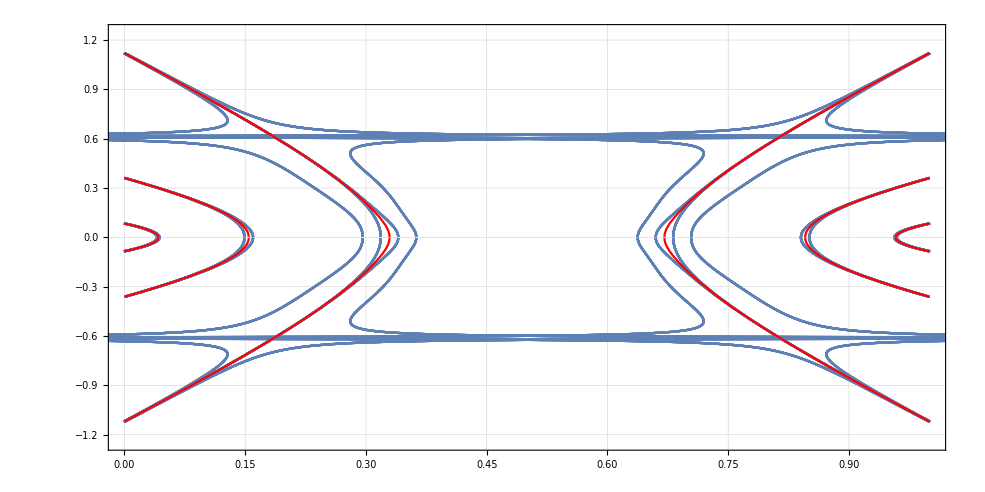
```mathematica
img=-Graphics-;
```

{{2.26055,1.85519},{2.15976,1.75016},{2.1961,1.69724},{2.19256,1.6},{2.5033,1.8642}}

{{2.26709,-25.0083},{2.13718,-22.2419},{0.9719,-22.0414},{-0.209586,-20.7354},{-1.10245,-28.5948}}

{{2383.34,338.369},{1884.61,278.815},{1860.04,79.641},{1645.07,-112.658},{3121.46,-350.849}}

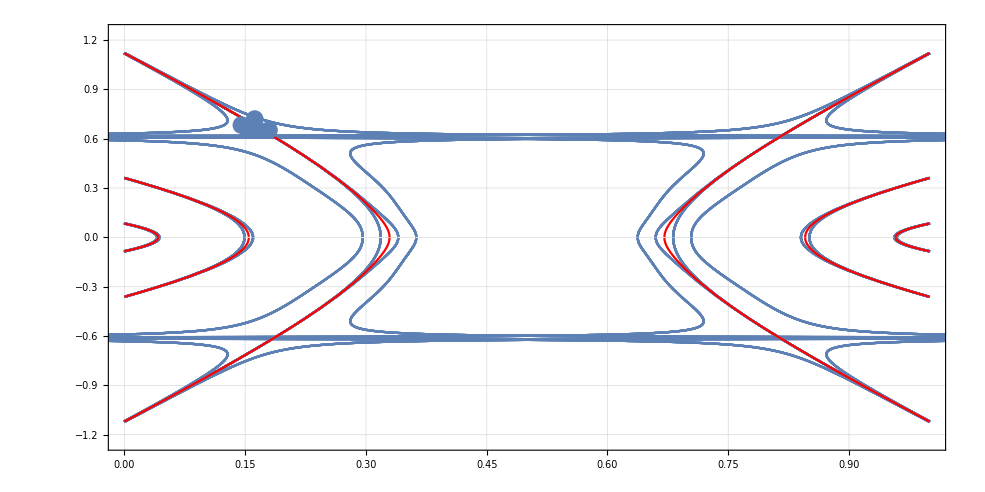

```mathematica
μ=3.8284;
{{0.149,0.04897},{0.1508,-0.03034}};

points = {{0.1452,0.6829},{0.1532,0.6591},{0.1644,0.6605},{0.1796,0.6522},{0.1618,0.7199}};
map1points = Table[ {Re[map[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}]
map2points = Table[ {Re[map2[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map2[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}]
map3points = Table[ {Re[map3[points⟦i,1⟧,points⟦i,2⟧,μ]],Im[map3[points⟦i,1⟧,points⟦i,2⟧,μ]]},{i,1,Length[points]}]

Show[img,ListPlot[points],ListPlot[map1points,PlotStyle->Red],ListPlot[map2points,PlotStyle->Green],ListPlot[map3points,PlotStyle->Blue]]
```

```mathematica
N[{{"0.3657","0.846"},{"0.6171","0.8561"},{"0.5867","0.1952"},{"0.4239","0.2621"}}]
```

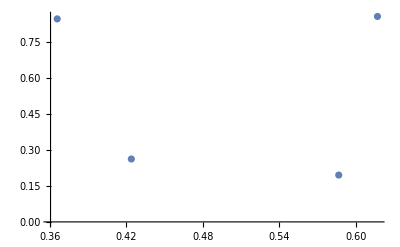

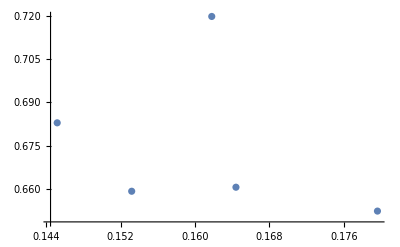
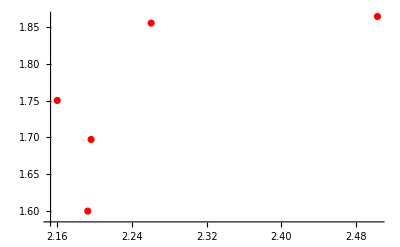
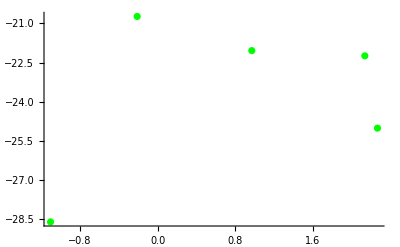
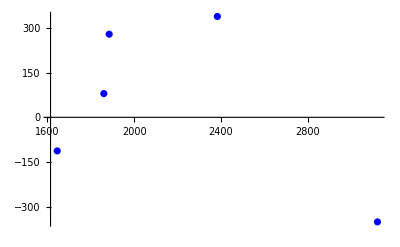
Show[img,-Graphics-,-Graphics-,-Graphics-,-Graphics-]

{{2383.34,338.369},{1884.61,278.815},{1860.04,79.641},{1645.07,-112.658},{3121.46,-350.849}}

{{2.26709,-25.0083},{2.13718,-22.2419},{0.9719,-22.0414},{-0.209586,-20.7354},{-1.10245,-28.5948}}

{{2.26055,1.85519},{2.15976,1.75016},{2.1961,1.69724},{2.19256,1.6},{2.5033,1.8642}}

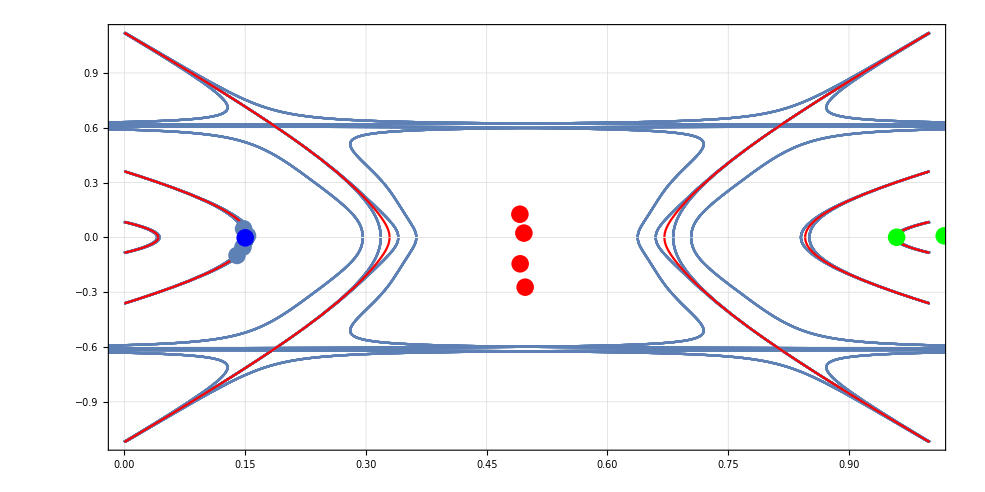

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

{{0.148,0.04702},{0.1529,0.008829},{0.1472,-0.05351},{0.1398,-0.09879}}

-Graphics-

```mathematica
ListPlot[ToExpression[{{"0.3657","0.846"},{"0.6171","0.8561"},{"0.5867","0.1952"},{"0.4239","0.2621"}}]]
```

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

-Graphics-

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

-Graphics-

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

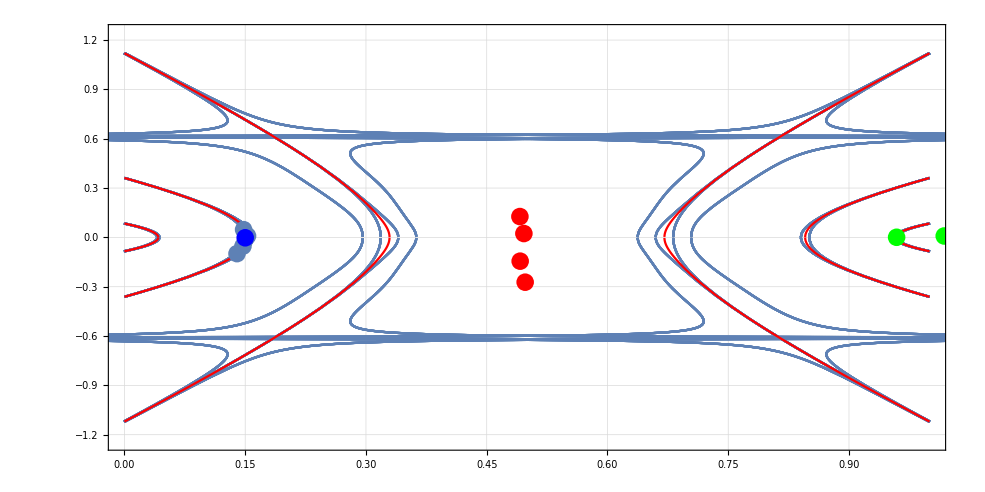

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

-Graphics-

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

-Graphics-

{{-0.0710167,-0.0338473},{0.149999,-0.00242617},{-0.145805,0.0384438},{-1.14651,0.0266294}}

{{1.01829,0.00852915},{0.959151,0.00069011},{1.03682,-0.00935305},{1.24128,-0.00469171}}

{{0.49121,0.126728},{0.496159,0.0234646},{0.491549,-0.144548},{0.497751,-0.272461}}

{{0.148,0.04702},{0.1529,0.008829},{0.1472,-0.05351},{0.1398,-0.09879}}

-Graphics-

```mathematica
map1points
map2points
map3points
```

```mathematica
N[{{"0.148","0.04702"},{"0.1529","0.008829"},{"0.1472","-0.05351"},{"0.1398","-0.09879"}}]
```

{{0.148,0.04702},{0.1529,0.008829},{0.1472,-0.05351},{0.1398,-0.09879}}